```mathematica
(*Pressure in bars*)
P={1.013,1.034,1.103,1.172,1.241,1.31,1.379,1.517,1.655,1.793,1.931,2.068,2.206,2.344,2.482,2.62,2.758,2.896,3.034,3.172,3.309,3.447,3.585,3.723,3.861,3.999,4.137,4.275,4.413,4.551,4.688,4.826,4.964,5.102,5.24,5.378,5.516,5.654,5.792,5.929,6.067,6.205,6.343,6.481,6.619,6.757,6.895,7.239,7.584,7.929,8.274,10.34,12.07,13.79,15.51,17.24,18.96,20.68,22.41,24.13,25.86,27.58,29.3,31.03,32.75,34.47,36.2,37.92,39.64,41.37,43.09,44.82,46.54,48.26,49.99,51.71,53.43,55.16,56.88,58.61,60.33,62.05,65.5,68.95,75.06,84.64,98.78,114.6,127.9,147.3,163.3,186.8,213.5,222.4};
(*Boiling point in Celsius*)
TC={100,101,102,104,106,107,109,112,114,117,119,121,123,125,127,129,131,132,134,135,137,138,140,141,142,144,145,146,147,148,149,151,152,153,154,155,156,157,158,158,159,160,161,162,163,164,164,166,168,170,172,181,189,194,200,205,210,214,218,222,226,229,233,236,239,242,245,247,250,252,255,257,260,262,264,266,268,270,272,274,276,278,281,285,290,298,310,321,329,341,349,360,371,374};
```

FittedModel[6552.52 ⅇ^(-1282.73/T)]

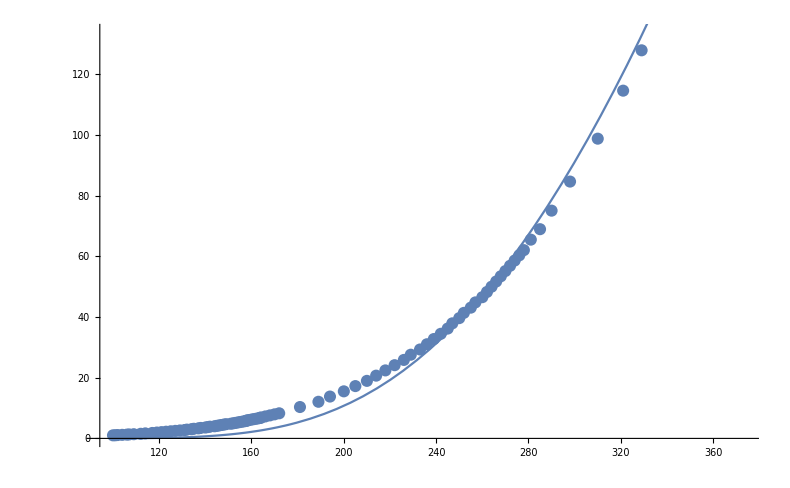

10665.9

```mathematica
data = Thread[{TC,P}];
nlm=NonlinearModelFit[data,A ⅇ^(-b/T),{A,b},T]
Show[ListPlot[data],Plot[nlm[T],{T,100,380}]]
1282.73*8.315
```

{-40,-20,0.01,25,50,100,150,200,250,300,350,374}

{0.00013,0.00103,0.00612,0.0317,0.1234,1.013,4.757,15.54,39.74,85.84,165.2,220.6}

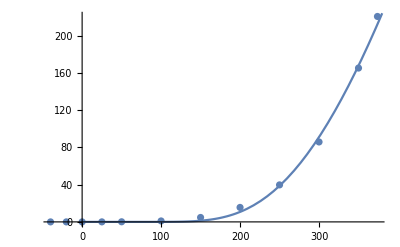

```mathematica
temp={-40,-20,0.01,25,50,100,150,200,250,300,350,374}
pressure={0.00013,0.00103,0.00612,0.0317,0.1234,1.013,4.757,15.54,39.74,85.84,165.2,220.6}
data=Thread[{temp,pressure}];
Show[ListPlot[data],Plot[nlm[x],{x,-40,380}]]
```

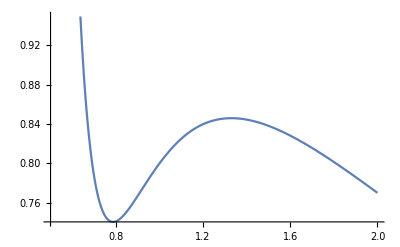

```mathematica
vanderwaals[t_,v_]:=(8t)/(3v-1)-3/v^2
Plot[vanderwaals[0.95,v],{v,0.5,2}]
```

2/729 (-9/v+(4 t)/(-1+3 v)-4 t Log[-1+3 v])

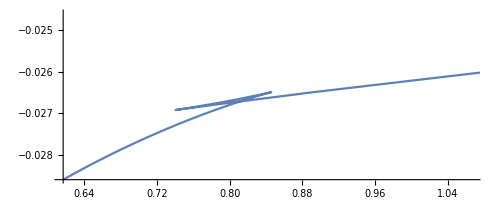

```mathematica
T=Tc t;
V=Vc v;
Vc=3 n b;
Pc=1/27 a/b^2;
Tc=8/27 a/(k b);
b=1;
a=1;
n=1;
gibbs[v_,t_]=FullSimplify[(-n k T Log[V-n b]+n k T n b/(V-n b)-2a n^2/V)Pc]
ParametricPlot[{vanderwaals[0.95,v],gibbs[v,0.95]},{v,0.5,3}]
```

```mathematica
Clear[Tc]
```